```mathematica
(* Charlie liu ,2020/June/Beijing *)
ClearAll;
img=-Graphics-;
Manipulate[ImageRotate[img,-a Degree],{a,-30,30}]
```

```mathematica
img=-Graphics-;
points={};
curvatures={};
GetList[i_,points_]:=Module[{},ClearAll[list];list={};
Row[{Manipulate[Grid[{{"Selected Points","Sample List"},{Show[i,Graphics[{Point[u]}],ImageSize->ImageDimensions[i]],Dynamic[If[(ValueQ[list]==False)||(list=={}),"1. move bottom-left and upper-right red points\n2. set each coordinate\n3. add/del points if necessary(alt+click/cmd+click?\n4. click Calculate button",list=Round[#,accuracy]&/@list;
Sort[RandomSample[list,UpTo[10]]]//TableForm]]}}],Row[{Dynamic[u[[1]]],"->",Control[{coordinate1,{{0,0}},InputField,ImageSize->80}],Dynamic[u[[2]]],"->",Control[{coordinate2,{{1,1}},InputField,ImageSize->80}],Control[{{accuracy,0.01},InputField,ImageSize->50}]},"  "],Row[{Button["Calculate",{list=locator2coordinate[u,{coordinate1,coordinate2}];
};,ImageSize->120]},"  "],Row[{Button["Clear points",u=Take[u,2];Put[u,"locator"],ImageSize->120]},"  "],{{u,Join[{{1,1},ImageDimensions[i]-{1,1}},Sort[points]]},Locator,LocatorAutoCreate->True,Appearance->Style["●",Red,8]},ControlPlacement->{Bottom,Bottom}]},"  "]]

locator2coordinate[list_,sample_]:=Module[{a,b,c,d,mat,cnst,solve,matx,cnstx},mat={{a,0},{0,d}};cnst={b,c};
solve=Solve[mat.list[[1]]+cnst==sample[[1]]&&mat.list[[2]]+cnst==sample[[2]],{a,b,c,d}];
matx=mat/.solve;cnstx=cnst/.solve;
Partition[Flatten[(matx.#+cnstx)&/@list],2]//Sort]
fining=img;
GetList[fining,points]
```

{{135.,317.5},{141.36,302.05},{150.44,291.1},{165.,282.05},{172.26,272.95},{187.72,262.95},{199.54,258.4},{213.18,257.5},{226.82,257.5},{238.62,260.2},{252.26,266.55},{262.26,273.85},{269.54,283.85},{275.9,292.05},{280.44,301.1},{285.8,310.}}

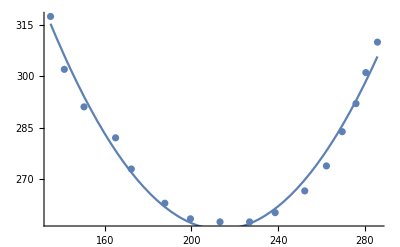

FittedModel[698.276-4.14619 x+0.00970256 x^2]

0.999912

{0.999912, | DF | SS | MS
Model | 3 | 1.26562×10^6 | 421874.
Error | 13 | 110.827 | 8.52514
Uncorrected Total | 16 | 1.26573×10^6 | 
Corrected Total | 15 | 5949.57 | }

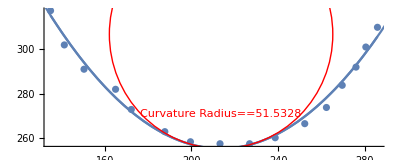

```mathematica
list
 da2=list;

g1=ListPlot[da2];
Fit[da2,{1,x,x^2},x];
f=%;
g2=Plot[f,{x,First@First@da2,First@Last@da2}] ;  
Show[g1,g2]
nlm=NonlinearModelFit[da2,u+v*x+w*x^2,{u,v,w},x]
nlm[ "RSquared" ]
nlm[{"RSquared","ANOVATable"}]

cur1[f0_]:=Module[ {x0,r0},
x0= x/.Last[FindMinimum[f0,{x,0}]];
(* First@Flatten[FindMinimum[f0,{x,0}] ]  *)
(* ArcCurvature[f0,x] *)
(*Simplify[ArcCurvature[f0,x]/.x->x0,x0∈Reals] *)
r0=1/Simplify[ArcCurvature[f0,x]/.x->x0,x0∈Reals];
Show[Plot[f0,{x,x0-2*r0,x0+2*r0}],Graphics[{Red,Circle[{x0,First@Flatten[FindMinimum[f0,{x,0}] ]+r0},r0],Inset[Curvature Radius==r0,{x0,First@Flatten[FindMinimum[f0,{x,0}] ]+0.3*r0}]}]]
] 
curv0[f0_]:=Module[ {x0,r0},
x0= x/.Last[FindMinimum[f0,{x,0}]];
r0=1/Simplify[ArcCurvature[f0,x]/.x->x0,x0∈Reals]
] 
 g3=cur1[f] ;
Show[g1,g2,g3,AspectRatio->0.4]
```